```mathematica
(*гр. 221703*)
(*Гаврилович Алиса*)
(*Вариант 3*)
(*Задание №1*)
f[x_]:=66 x^3-49 x^2-209x-84
```

```mathematica
(*отделим графические корни уравнения*)
```

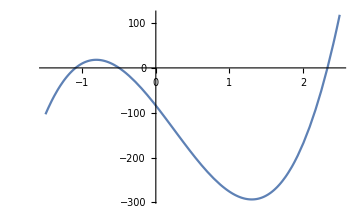

```mathematica
Plot[f[x],{x,-1.5,2.5},AxesOrigin->{0,0},ImageSize->Medium]
```

```mathematica
(*по графику видно,что уравнение имеет три действительных корня,они расположены в интервалах (-1.5,-1),(-1,0),(2,2.5)*)
```

```mathematica
(*найдем один из корней заданного уравнение с точностью 10^-3 методом хорд*)
(*доведем до заданной точности корень,располоденный в отрезке (-2,-1)*)
a=-2;
b=-1;
e=0.001;
f[a]
f[b]
```

-390

10

-98+396 x

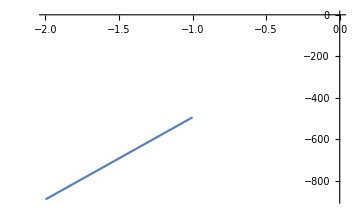

```mathematica
pr2=D[f[x],{x,2}]
Plot[pr2,{x,-2,-1},AxesOrigin->{0,0},ImageSize->Medium]
```

```mathematica
(*т.к. на отрезке (-2,-1) значение функции в точке a отрицательно и ее вторая производная отрицательна,то возьмем x0 как b    (f(a)*f"(x)>0)      *)
```

Решение x=-1.08912 получено на 12 шаге

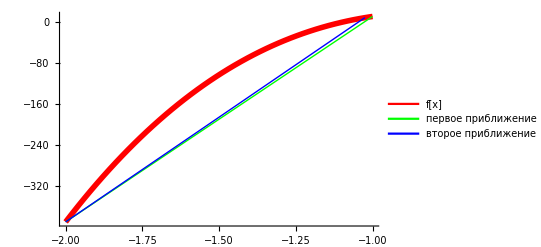

```mathematica
xprev=0;
xn=0;
xnext=b;
Do[xprev=xn;
xn=xnext;
xnext=a-f[a]/(f[xnext]-f[a])*(xnext-a)//N;
If[Abs[xn-xprev]<e,
Print["Решение x=",xn," получено на ",iter," шаге"];
Break[]],{iter,1,100}];
gr=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
line1=Line[{{a,f[a]},{b,f[b]}}];
xnext=a-f[a]/(f[b]-f[a])*(b-a);
line2=Line[{{a,f[a]},{xnext,f[xnext]}}];
Legended[Show[gr,Graphics[{Green,line1,Blue,line2}]],LineLegend[{Red,Green,Blue},{"f[x]","первое приближение","второе приближение"}]]
```

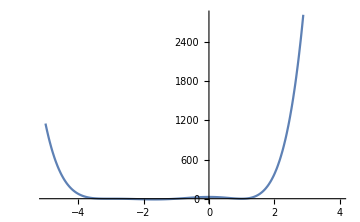

```mathematica
(*Задание №2*)
Clear[f]
f[x_]:=x^6+8 x^5+17 x^4-8 x^3-45 x^2+27;
Plot[f[x],{x,-5,4},AxesOrigin->{0,0},ImageSize->Medium]
```

```mathematica
(*С помощью встроенных функций Solve,NSolve,Roots,FindRoot найдем корни алгебраического уравнения f(x)=0*)
```

```mathematica
N[Solve[f[x]==0,x]]
N[NSolve[f[x]==0,x]]
N[Roots[f[x]==0,x]]
N[FindRoot[f[x]==0,{x,1}]]
(*С помощью встроенной функции Factor разложим многочлен f(x) на множители*)
Factor[f[x]]
```

{{x→-3.},{x→-3.},{x→-3.},{x→-1.},{x→1.},{x→1.}}

{{x→-3.},{x→-3.},{x→-3.},{x→-1.},{x→1.},{x→1.}}

x==-3.||x==-3.||x==-3.||x==-1.||x==1.||x==1.

{x→1.}

(-1+x)^2 (1+x) (3+x)^3

```mathematica
(*Задание 3*)
```

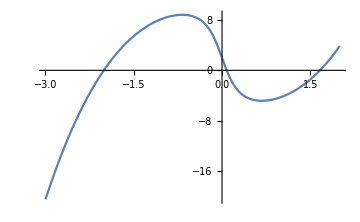

```mathematica
Clear[f,a,b]
f[x_]:=x^3+2*x+2-7*ArcTan[4*x];
(*отделим графические корни уравнения*)
Plot[f[x],{x,-3,2},AxesOrigin->{0,0},ImageSize->Medium]
```

-20.5864

0.125089

6 x+(896 x)/((1+16 x^2)^2)

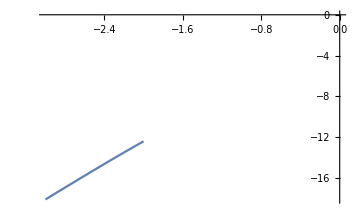

```mathematica
(*по графику видно,что уравнение имеет три действительных корня,они расположены в интервалах (-3,-2),(0,1),(1,2)*)

(*пункт а*)

(*найдем один из корней заданного уравнение с точностью 10^-3 методом Ньютона*)
(*доведем до заданной точности корень,расположенный в отрезке (-3,-2)*)
a=-3;
b=-2;
N[f[a]]
N[f[b]]
pr2=D[f[x],{x,2}]
Plot[pr2,{x,-3,-2},AxesOrigin->{0,0},ImageSize->Medium]
```

```mathematica
(*т.к. на отрезке (-3,-2) значение функции в точке a отрицательно и ее вторая производная в точке а тоже отрицательна,то возьмем x0 как a     (f(x0)*f"(x0)>0)   *)
```

```mathematica
x0=a;
xApproximation;
Do[xn=x0;
x0=N[x0-f[x0]/f'[x0]];
If[Abs[xn-x0]<e,
Print["Решение x=",xn," получено на ",iter," шаге."];
xApproximation=xn;
Break[]],
{iter,1,100}]
```

Решение x=-2.00957 получено на 4 шаге.

```mathematica
(*пункт б*)
```

```mathematica
(*найдем методом секущих*)
```

```mathematica
x0=a;
xn=xApproximation;
Do[
xprev=xn;
xn=x0;
x0=N[x0-f[x0]*((x0-xprev)/(f[x0]-f[xprev]))];
If[Abs[xn-x0]<e,
Print["Решение x=",xn," получено на ",iter," шаге."];
Break[]],
{iter,1,100}]
```

Решение x=-2.00931 получено на 2 шаге.

```mathematica
(*Задание 4*)
```

```mathematica
(*Метод релаксации*)
```

```mathematica
λ=0.1;
g[x_]:=x-λ*f[x];
xn=a;
xprev=xn-0.1;
iter=0;
While[Abs[xn-xprev]>e,xprev=xn;xn=g[xn];iter++];
Print["Решение x=",xn," получено на ",iter," шаге."];
```

Решение x=-2.00932 получено на 9 шаге.

```mathematica
(*Задание 5*)
(*С помощью встроенных функций Solve,NSolve,Roots,FindRoot найдем корни алгебраического уравнения φ(x)=0*)
Clear[f]
```

```mathematica
f[x_]:=x^3+2*x+2-7*ArcTan[4*x];
```

```mathematica
Plot[f[x],{x,-3,2},AxesOrigin->{0,0},ImageSize->Medium]
```

-Graphics-

```mathematica
Solve[f[x]==0,x]
NSolve[f[x]==0,x]
FindRoot[f[x]==0,{x,-2}]
FindRoot[f[x]==0,{x,0}]
FindRoot[f[x]==0,{x,2}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[2+2 x+x^3-7 ArcTan[4 x]==0,x]

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[2+2 x+x^3-7 ArcTan[4 x]==0,x]

{x→-2.00918}

{x→0.0796832}

{x→1.66568}

```mathematica
(*Задание 6*)
```

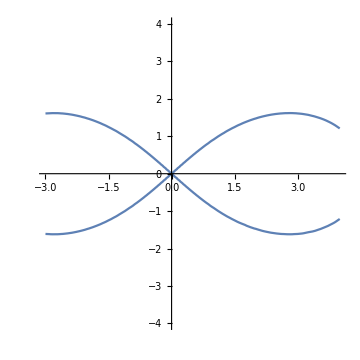

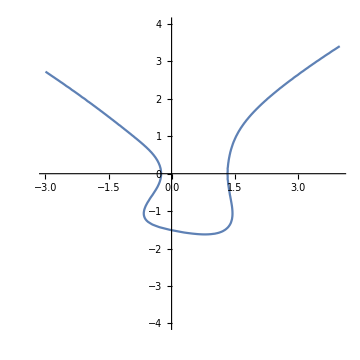

```mathematica
Clear[f]
f[x_,y_]:=(x^2+y^2)^2-21(x^2-y^2);
g[x_,y_]:=2 x^4-3 y^2-4x-y^5-1;
gr1=ContourPlot[f[x,y]==0,{x,-3,4},{y,-4,4},Axes->True,Frame->False,ImageSize->Medium]
gr2=ContourPlot[g[x,y]==0,{x,-3,4},{y,-4,4},Axes->True,Frame->False,ImageSize->Medium]
```

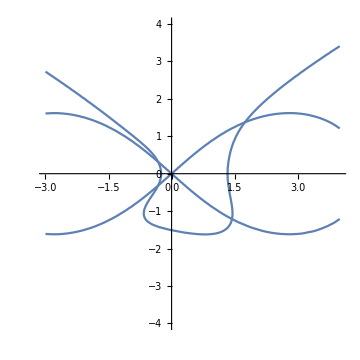

```mathematica
Show[gr1,gr2,ImageSize->Medium]
```

```mathematica
(*по графику видно,что кривые пересекаются в 4 точках,эти точки будем использовать для начального приближения*)
FindRoot[{f[x,y]==0,g[x,y]==0},{x,2},{y,1}]
FindRoot[{f[x,y]==0,g[x,y]==0},{x,1},{y,-1}]
FindRoot[{f[x,y]==0,g[x,y]==0},{x,-1},{y,-1}]
FindRoot[{f[x,y]==0,g[x,y]==0},{x,-1},{y,1}]
```

{x→1.74447,y→1.37337}

{x→1.43746,y→-1.21268}

{x→-0.318845,y→-0.315802}

{x→-0.321501,y→0.318382}